```mathematica
{{cSVOKp[G],cSVOKp[L],cSVOKp[P]},{cSVQEDp[G],cSVQEDp[L],cSVQEDp[P]}}=<<"~/Physik/PhD/MMa/data/ElProduction.cSVp.m";
```

```mathematica
rep=Module[{vs,solβ,sols,vq,solβq,solq},
vs={ρ-> 4m2/s,β-> Sqrt[1-ρ],χ-> (1-β)/(1+β)};
solβ=Solve[χ==(χ/.vs),β][[1,1]];
sols=Solve[χ==(χ//.vs),s][[1,1]];
vq={ρq-> 4m2/q2,βq-> Sqrt[1-ρq],χq-> (βq-1)/(βq+1)};
solβq=Solve[χq==(χq/.vq),βq][[1,1]];
solq=Solve[χq==(χq//.vq),q2][[1,1]];
{sp-> s-q2,u1-> -sp-t1,t1->-sp/2(1-β ct1)/.solβ,sols,solq,solβ,solβq}
]
```

{sp→-q2+s,u1→-sp-t1,t1→-1/2 sp (1-(ct1 (1-χ))/(1+χ)),s→(m2 (1+χ)^2)/χ,q2→-(m2 (-1+χq)^2)/χq,β→(1-χ)/(1+χ),βq→(-1-χq)/(-1+χq)}

```mathematica
Module[{e,f,ff,Nx,xs,data,fitpol,fitpolsol,fitcos},
e=cSVQEDp@L/.{ln[βtil]-> 0};
f=Dot@@Transpose@e;
f=f//.rep;
ff=f/.{m2-> 1}/.{ct1-> 0}/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]};
ff=ff;
Print@N@Series[ff,{χ,0,2},{χq,0,2},Assumptions-> {0<χ<1,0<χq<1}];
Print@N@Series[ff,{χq,0,2},{χ,0,2},Assumptions-> {0<χ<1,0<χq<1}];
Print@N@Series[ff,{χ,1,2},{χq,1,3},Assumptions-> {0<χ<1,0<χq<1}];
(*f=Together@f;
f=FullSimplify@f;*)
(*Print[{Simplify[f/.{χ-> 0}],Simplify[f/.{χ-> 1}]}];
Print[{Simplify[f/.{χq-> 0}],Simplify[f/.{χq-> 1}]}];
Print[{Simplify[f/.{ct1-> -1}],Simplify[f/.{ct1-> 1}]}];*)

(*ff=f/.{m2-> 1.}/.{χ-> 1/2,χq-> 1/2}/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]};
Nx=500;
xs=Table[-1+2j/N,{j,0,N}];
data={#,ff/.{ct1-> #}}&/@xs;
fitpol=Fit[data,{1,ct1^2,ct1^4,ct1^6,ct1^8},ct1];
Print@fitpol;
fitcos=Fit[data,{1,Cos[ct1],Cos[ct1]^2,Cos[ct1]^3,Cos[ct1]^4,Cos[ct1]^5},ct1];
Print@fitcos;
{Show[ListPlot[data, PlotStyle->Green],Plot[{fitpol,fitcos,ff},{ct1,-1,1}],ImageSize-> 500],Show[LogPlot[{Abs[(ff-fitpol)/ff],Abs[(ff-fitcos)/ff]},{ct1,-1,1}],ImageSize-> 500]}*)

]
```

((1107.18-402.124 Log[χ]-804.248 Log[χq])/(χq+0.)+(-2214.36+804.248 Log[χ])+(1107.18-402.124 Log[χ]+804.248 Log[χq]) (χq+0.)+O[χq+0.]^3) (χ+0.)+((-5276.02+804.248 Log[χq])/(χq+0.)^2+(19932.9+1114.92 Log[χ]+1206.37 Log[χ]^2+3216.99 Log[χq]-804.248 Log[χq]^2)/(χq+0.)+(-29313.8-2229.85 Log[χ]-2412.74 Log[χ]^2+1608.5 Log[χq]^2)+(19932.9+1114.92 Log[χ]+1206.37 Log[χ]^2-3216.99 Log[χq]-804.248 Log[χq]^2) (χq+0.)+(-5276.02-804.248 Log[χq]) (χq+0.)^2+O[χq+0.]^3) (χ+0.)^2+O[χ+0.]^3

((135.039-2970.21 Log[χ]-1608.5 Log[χ]^2+1763.83 Log[χq]+1608.5 Log[χ] Log[χq])/(χ+0.)+(2428.23+3034.1 Log[χ]+3619.11 Log[χ]^2-3527.67 Log[χq]-3216.99 Log[χ] Log[χq])+(3162.66-5912.85 Log[χ]-6031.86 Log[χ]^2+1763.83 Log[χq]+4825.49 Log[χ] Log[χq]) (χ+0.)+(-10245.5+11429.8 Log[χ]+8042.48 Log[χ]^2-6433.98 Log[χ] Log[χq]) (χ+0.)^2+O[χ+0.]^3) (χq+0.)+(-(128. (18.3171-33.8431 Log[χ]-25.1327 Log[χ]^2+27.5599 Log[χq]+25.1327 Log[χ] Log[χq]))/(χ+0.)^2-(42.6667 (6.61927-72.4033 Log[χ]+94.2478 Log[χ]^2-27.8342 Log[χq]-75.3982 Log[χ] Log[χq]))/(χ+0.)+42.6667 (-398.228+123.374 Log[χ]+188.496 Log[χ]^2+109.691 Log[χq]-150.796 Log[χ] Log[χq])-42.6667 (-331.718+174.637 Log[χ]+263.894 Log[χ]^2-27.8342 Log[χq]-226.195 Log[χ] Log[χq]) (χ+0.)-3.55556 (2717.45-2685.1 Log[χ]-3392.92 Log[χ]^2+992.156 Log[χq]+2714.34 Log[χ] Log[χq]) (χ+0.)^2+O[χ+0.]^3) (χq+0.)^2+O[χq+0.]^3

(-496.1 (χq-1.)^2+496.1 (χq-1.)^3+O[χq-1.]^4) (χ-1.)+((108.685-631.655 ⅈ) (χq-1.)^2-(108.685-631.655 ⅈ) (χq-1.)^3+O[χq-1.]^4) (χ-1.)^2+O[χ-1.]^3

1.77778 (127.817-18.8496 Log[χ]) (χ+0.)-0.296296 (3242.75-313.572 Log[χ]-339.292 Log[χ]^2) (χ+0.)^2+0.037037 (67176.9-4242.05 Log[χ]-18246.4 Log[χ]^2) (χ+0.)^3+O[χ+0.]^4

-39.6715 (χ-1.)+(8.59733-50.5113 ⅈ) (χ-1.)^2+(0.915738+50.5113 ⅈ) (χ-1.)^3+O[χ-1.]^4

{a→-31.91,b→-761.923,c→-1702.61,g→238.929,h→-1815.44,j→-549.815,b1→2.66391,c1→12.3632,h1→3.8897,j1→13.4249}

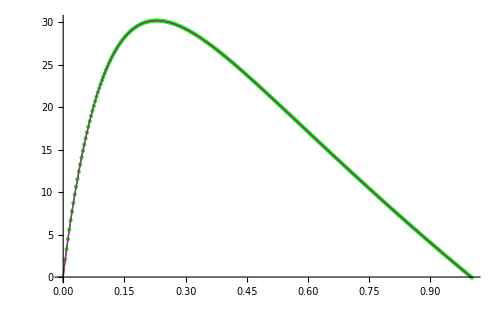
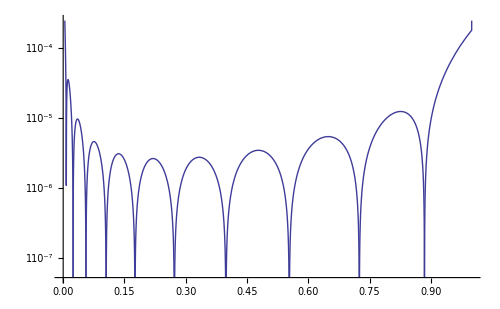

```mathematica
Module[{e,f,ff,Nx,xs,data,fitpol,fitpolsol,fitcos},
Needs["FunctionApproximations`"];
e=cSVQEDp@L/.{ln[βtil]-> 0};
f=Dot@@Transpose@e;
f=f//.rep;
ff=f/.{m2-> 1}/.{ct1-> 0,χq-> 3/4}/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]};
ff=ff;
Print@N@Series[ff,{χ,0,3},Assumptions-> {0<χ<1}];
Print@N@Series[ff,{χ,1,3},Assumptions-> {0<χ<1}];
ff=N@ff;
Nx=300;
xs=Table[(j+1/2)/Nx,{j,Nx}];
data={#,ff/.{χ-> #}}&/@xs;
(*fitpol[χ_]=(a+b χ+d χ^2+h χ^4)Exp[-g*g χ];
fitpolsol=FindFit[data,fitpol@χ,{a,b,c,d,g,h},χ];*)
fitpol[χ_]=χ Log[χ](a+b χ+c χ^2)/(1+b1 χ+c1 χ^2) + χ(1-χ)(g + h χ + j χ^2)/(1+h1 χ+j1 χ^2);
fitpolsol=FindFit[data,fitpol@χ,{a,b,c,g,h,j,b1,c1,h1,j1},χ,MaxIterations-> 5000];
Print[fitpolsol];
{Show[ListPlot[data, PlotStyle->Green],Plot[{(fitpol@χ/.fitpolsol),ff},{χ,0,1}],ImageSize-> 500],Show[LogPlot[{Abs[(ff-(fitpol@χ/.fitpolsol))/ff]},{χ,0,1}],ImageSize-> 500]}
]
```

0.253968 (8239.51+36.49 Log[χq]) (χq+0.)-0.042328 (305224.+5957.15 Log[χq]) (χq+0.)^2+0.00529101 (8.10963×10^6+280730. Log[χq]) (χq+0.)^3+O[χq+0.]^4

130.453 (χq-1.)^2-130.453 (χq-1.)^3+O[χq-1.]^4

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a→3.96527,b→2368.4,c→34615.2,g→2098.07,h→-74574.1,j→18512.8,b1→7.75727,c1→11.0185,h1→-35.4525,j1→5.59111}

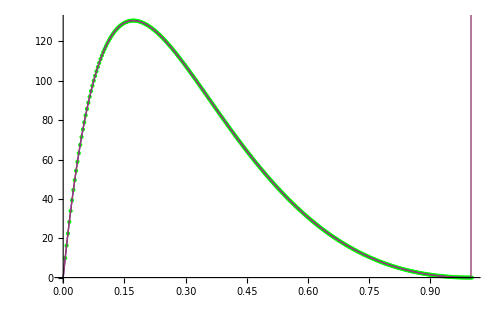
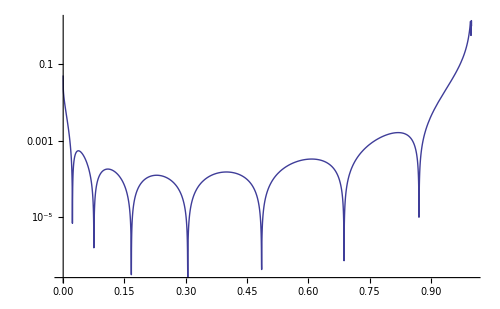

```mathematica
Module[{e,f,ff,Nx,xs,data,fitpol,fitpolsol,fitcos},
e=cSVQEDp@L/.{ln[βtil]-> 0};
f=Dot@@Transpose@e;
f=f//.rep;

ff=f/.{m2-> 1}/.{ct1-> 0,χ-> 3/4}/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]};
ff=ff;
Print@N@Series[ff,{χq,0,3},Assumptions-> {0<χq<1}];
Print@N@Series[ff,{χq,1,3},Assumptions-> {0<χq<1}];
ff=N@ff;
Nx=300;
xs=Table[(j+1/2)/Nx,{j,Nx}];
data={#,ff/.{χq-> #}}&/@xs;
(*fitpol=Fit[data,{1,χq,χq^2,χq^3,χq^4},χq];
Print[fitpol];*)
(*fitpol[χq_]=c (a+b χq+d χq^2+h χq^4)Exp[-g*g χq];*)
fitpol[χq_]=(a+b χq+c χq^2)/(1+b1 χq+c1 χq^2)χq Log[χq] + (g+h χq+j χq^2)/(1+h1 χq+j1 χq^2)χq (1-χq);
fitpolsol=FindFit[data,fitpol@χq,{a,b,c,g,h, j,b1,c1,h1,j1},χq,MaxIterations-> 5000];
Print[fitpolsol];
(*fitcos=Fit[data,{Sin[π χ],Sin[π χ]^2,Sin[π χ]^3,Sin[π χ]^4,Sin[π χ]^5},χ];
Print@fitcos;*)
{Show[ListPlot[data, PlotStyle->Green],Plot[{(fitpol@χq/.fitpolsol),ff},{χq,0,1}],ImageSize-> 500],Show[LogPlot[{Abs[(ff-(fitpol@χq/.fitpolsol))/ff]},{χq,0,1}],ImageSize-> 500]}
]
```

{a$245768[0,0]→-5.23927×10^6,b$245768[0,0]→-529305.,c$245768[0,0]→-1.18581×10^6,a$245768[0,1]→-1.12675×10^7,b$245768[0,1]→4.48392×10^6,c$245768[0,1]→-1.15037×10^7,a$245768[0,2]→-3.19907×10^7,b$245768[0,2]→-1.09461×10^7,c$245768[0,2]→-3.84622×10^6,a$245768[0,3]→2.09504×10^7,b$245768[0,3]→7.99035×10^6,c$245768[0,3]→1.65361×10^7,a$245768[1,0]→9.96041×10^7,b$245768[1,0]→2.14771×10^7,c$245768[1,0]→7.67142×10^6,a$245768[1,1]→-3.55155×10^8,b$245768[1,1]→-1.47122×10^8,c$245768[1,1]→8.21996×10^7,a$245768[1,2]→1.13912×10^9,b$245768[1,2]→3.07303×10^8,c$245768[1,2]→3.16467×10^7,a$245768[1,3]→-7.36455×10^8,b$245768[1,3]→-1.99696×10^8,c$245768[1,3]→-1.21521×10^8,a$245768[2,0]→7.97934×10^7,b$245768[2,0]→1.25154×10^8,c$245768[2,0]→-1.49176×10^7,a$245768[2,1]→-1.37996×10^9,b$245768[2,1]→-9.42461×10^8,c$245768[2,1]→-1.69369×10^8,a$245768[2,2]→2.32176×10^9,b$245768[2,2]→2.10123×10^9,c$245768[2,2]→-7.21506×10^7,a$245768[2,3]→-1.65628×10^9,b$245768[2,3]→-1.43329×10^9,c$245768[2,3]→2.56445×10^8,a$245768[3,0]→4.80174×10^7,b$245768[3,0]→7.39149×10^7,c$245768[3,0]→8.9366×10^6,a$245768[3,1]→9.6075×10^7,b$245768[3,1]→-5.77133×10^8,c$245768[3,1]→1.05318×10^8,a$245768[3,2]→2.90923×10^8,b$245768[3,2]→1.31631×10^9,c$245768[3,2]→4.79684×10^7,a$245768[3,3]→-1.66913×10^8,b$245768[3,3]→-9.12012×10^8,c$245768[3,3]→-1.62228×10^8}

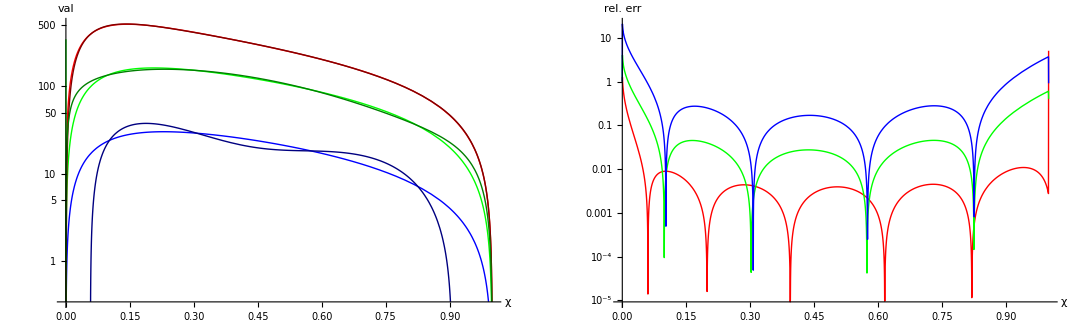

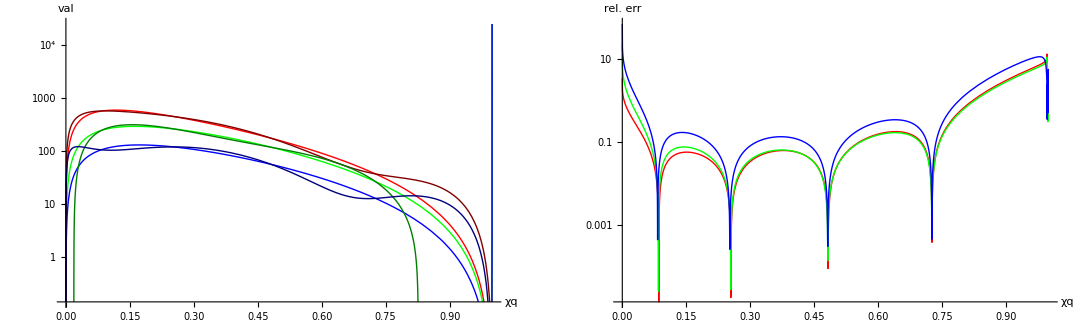

```mathematica
Module[{e,f,ff,N1,N2,xs,data,fitpol,fitpolsol,fitcos,Nj,Nk,a,b,c,d},
e=cSVQEDp@L/.{ln[βtil]-> 0};
f=Dot@@Transpose@e;
f=f//.rep;

ff=f/.{m2-> 1.}/.{ct1-> 0}/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]};
ff=ff;
N1=150;
N2=150;
xs=Table[{(j+1/2)/N1,(k+1/2)/N2},{j,N1-1},{k,N2-1}];
xs=Flatten[xs,1];
data={#[[1]],#[[2]],ff/.{χ->#[[1]],χq-> #[[2]]}}&/@xs;

(*fitpol[χ_,χq_]=a χ(1-χ) χq^(1)(1-χq)^2Exp[-g*g χq]Exp[-h*h χ]*
(c00+c10 χ+c01 χq+c11 χ χq+c20 χ^2 + c02 χq^2 + c21 χ^2 χq + c12 χ χq^2+c22 χ^2 χq^2+c40 χ^4+c41 χ^4 χq + c42 χ^4 χq^2 + c44 χ^4 χq^4+ c24 χ^2 χq^4+c14 χ χq^4+c04 χq^4);
fitpolsol=FindFit[data,fitpol[χ,χq],{a,
c00,c10,c01,c11,c20,c02,c21,c12,c22,c40,c41,c42,c44,c24,c14,c04,
{g,2},{h,2}},{χ,χq}];*)
(*fitpol[χ_,χq_]=a χ (1-χ) χq Log[χq](1+a10 χ+a01 χq+a11 χ χq)+
b χ Log[χ] χq (1-χq)(1+b10 χ+b01 χq+b11 χ χq)+
c χ Log[χ] χq Log[χq](1+c10 χ+c01 χq+c11 χ χq)+
d χ(1-χ) χq (1-χq)(1+d10 χ+d01 χq+d11 χ χq);
fitpolsol=FindFit[data,fitpol[χ,χq],{a,a10,a01,a11,b,b10,b01,b11,c,c10,c01,c11,d, d10,d01,d11},{χ,χq}];*)
Nj=3;
Nk=3;
fitpol[χ_,χq_]=χ(1-χ)χq(1-χq)^2Sum[a[j,k]*χ^j*χq^k,{j,0,Nj},{k,0,Nk}]+
χ Log[χ]χq(1-χq)^2Sum[b[j,k]*χ^j*χq^k,{j,0,Nj},{k,0,Nk}]+
χ(1-χ)χq Log[χq] Sum[c[j,k]*χ^j*χq^k,{j,0,Nj},{k,0,Nk}](*+
χ Log[χ]χq Log[χq]Sum[d[j,k]*χ^j*χq^k,{j,0,Nj},{k,0,Nk}]*);
fitpolsol=FindFit[data,fitpol[χ,χq],Flatten@Table[{a[j,k],b[j,k],c[j,k](*,d[j,k]*)},{j,0,Nj},{k,0,Nk}],{χ,χq}];

Print[fitpolsol];
Print@GraphicsRow[{
LogPlot[Evaluate[(ff/.{χq-> {1/4,2/4,3/4}})~Join~(fitpol[χ,χq]/.fitpolsol/.{χq-> {1/4,2/4,3/4}})],{χ,0,1},AxesLabel-> {χ,"val"},PlotStyle->{Red,Green,Blue,Darker[Red,.5],Darker[Green,.5],Darker[Blue,.5]},ImageSize-> 500],
LogPlot[Evaluate[Abs[(ff-(fitpol[χ,χq]/.fitpolsol))/ff]/.{χq-> {1/4,2/4,3/4}}],{χ,0,1},AxesLabel-> {χ, "rel. err"},PlotStyle->{Red,Green,Blue},ImageSize-> 500]
}];
Print@GraphicsRow[{
LogPlot[Evaluate[(ff/.{χ-> {1/4,2/4,3/4}})~Join~(fitpol[χ,χq]/.fitpolsol/.{χ-> {1/4,2/4,3/4}})],{χq,0,1},AxesLabel-> {χq,"val"},PlotStyle->{Red,Green,Blue,Darker[Red,.5],Darker[Green,.5],Darker[Blue,.5]},ImageSize-> 500],
LogPlot[Evaluate[Abs[(ff-(fitpol[χ,χq]/.fitpolsol))/ff]/.{χ-> {1/4,2/4,3/4}}],{χq,0,1},AxesLabel-> {χq, "rel. err"},PlotStyle->{Red,Green,Blue},ImageSize-> 500]
}];
(*{Show[ListPlot3D[data,Mesh->All],ImageSize-> 500],
Show[Plot3D[{(fitpol[χ,χq]/.fitpolsol),ff},{χ,0,1},{χq,0,1}],ImageSize-> 500],
Show[Plot3D[{Log@Abs[(ff-(fitpol[χ,χq]/.fitpolsol))/ff]},{χ,0,1},{χq,0,1}],ImageSize-> 500]}*)
(*{Show[LogPlot[Evaluate[Abs[(ff-(fitpol[χ,χq]/.fitpolsol))/ff]/.{χq-> {1/4,1/2,3/4}}],{χ,0,1}],ImageSize-> 500],
Show[LogPlot[Evaluate[Abs[(ff-(fitpol[χ,χq]/.fitpolsol))/ff]/.{χ-> {1/4,1/2,3/4}}],{χq,0,1}],ImageSize-> 500]}*)
]
```